```mathematica
NuFlatPlate = (0.825+(0.387 Subscript[Ra, L]^(1/6))/((1+(0.492/Pr)^(9/16))^(8/27)))^2;
```

```mathematica
NuHorzCylinder = (0.6 + (0.387 Subscript[Ra, D]^(1/6))/((1+(0.559/Pr)^(9/16))^(8/27)))^2;
```

```mathematica
L = 5D; Subscript[Ra, L]=(g β (Tw-T0)L^3)/(ν α); Subscript[Ra, D] = (g β (Tw-T0) D^3)/(ν α);
```

```mathematica
hFlatPlate = NuFlatPlate κ/L // #/.Pr->0.71&
```

(κ (0.825+0.725426 ((D^3 g (-T0+Tw) β)/(α ν))^(1/6))^2)/(5 D)

```mathematica
hHorzCylinder = NuHorzCylinder κ/D // #/.Pr->0.71 &
```

(κ (0.6+0.321277 ((D^3 g (-T0+Tw) β)/(α ν))^(1/6))^2)/D

```mathematica
hRatio = hFlatPlate/hHorzCylinder // Simplify[#]&
```

((0.825+0.725426 ((D^3 g (-T0+Tw) β)/(α ν))^(1/6))^2)/(5 (0.6+0.321277 ((D^3 g (-T0+Tw) β)/(α ν))^(1/6))^2)

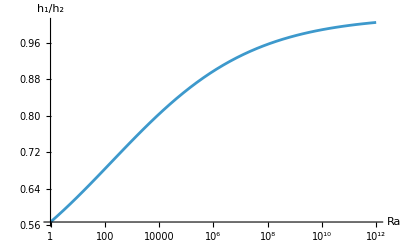

```mathematica
Plot[Evaluate[hRatio/.g->(Ra ν α/(β (Tw-T0)D^3))],{Ra,10^0,10^12},
AxesLabel->{Ra, Subscript[h, 1]/Subscript[h, 2]},ScalingFunctions->{"Log"},GridLines->Automatic]
```